# \[MathematicaIcon]Curva de Rotação ESO 116-G12\[MathematicaIcon]

## Utilitários

Massa Solar → Grama 


Kpc → Cm 

Densidades

## Tabelas

```mathematica
data= Import["C:\\Users\\Leoleo\\Desktop\\TCC\\Mathematica\\Fitting\\116.dat"];
Subscript[RC, total]=Table[{data[[i,1]],data[[i,3]]},{i,1,15}];
Subscript[RC, gas]=Table[{data[[i,1]],data[[i,4]]},{i,1,15}];
Erro = Table[data[[i,5]],{i,1,15}];
TableForm[data,TableHeadings->{{""},{"Raio","","Vtotal","Vgas","Erro"}}]
```

| Raio |  | Vtotal | Vgas | Erro
 | 0.295522 | 7.58904 | 20.94 | -0.234178 | 3.4
 | 0.985821 | 7.79329 | 39.95 | -1.95065 | 3.29
 | 1.62537 | 8.47973 | 51.54 | -1.68024 | 2.96
 | 2.18881 | 9.15955 | 67.92 | 5.43454 | 3.45
 | 3.17687 | 9.76846 | 80.22 | 13.5993 | 2.93
 | 3.76791 | 9.48569 | 83.33 | 18.0705 | 3.08
 | 4.35896 | 8.74732 | 91.38 | 21.8567 | 2.83
 | 4.8903 | 7.95629 | 101.65 | 24.2219 | 5.4
 | 6.19403 | 6.20847 | 104.77 | 27.7912 | 4.21
 | 7.16418 | 5.25717 | 108.62 | 29.5757 | 2.1
 | 8.0597 | 4.68539 | 108.48 | 30.9882 | 2.1
 | 8.95522 | 4.27244 | 108.73 | 33.3072 | 2.1
 | 9.85075 | 3.43065 | 110.24 | 36.6602 | 2.1
 | 10.7463 | 1.87414 | 110.63 | 38.4926 | 2.33
 | 11.6418 | 0.66706 | 111.52 | 36.585 | 4.74

## Valores de Parâmetros

```mathematica
Subscript[Tabela, Vdisk]=TableForm[Subscript[P, stars]= {{10^0.2,10^9},{10^0.3,10^9.8},{10^0.4,10^10.4},{10^0.7,10^11}},TableHeadings->{{"1","2","3","4"},{"R_d","M_d"}}];
Subscript[Tabela, Vdm]=TableForm[Subscript[P, dm]={{10^-0.5,4.1*10^8},{1,1.05*10^8},{10^0.5,2.5*10^7},{10^0.8,9.7*10^6},{10,5.7*10^6},{10^1.2,3.9*10^6},{10^1.4,2.3*10^6},{10^1.6,1.4*10^6}},TableHeadings->{{"Dwarf Spiral","","","Spiral Galaxy"},{"R_0","P_0"}}];
G:=4.302/10^6;

{Subscript[Tabela, Vdisk],Subscript[Tabela, Vdm]}
```

{ | R_d | M_d
1 | 1.58489 | 1000000000
2 | 1.99526 | 6.30957×10^9
3 | 2.51189 | 2.51189×10^10
4 | 5.01187 | 100000000000, | R_0 | P_0
Dwarf Spiral | 0.316228 | 4.1×10^8
 | 1 | 1.05×10^8
 | 3.16228 | 2.5×10^7
Spiral Galaxy | 6.30957 | 9.7×10^6
 | 10 | 5.7×10^6
 | 15.8489 | 3.9×10^6
 | 25.1189 | 2.3×10^6
 | 39.8107 | 1.4×10^6}

## Conversor de Unidades

```mathematica
ConversorKpc =DynamicModule[{a=0,b=0},Deploy[Style[Panel[Grid[Transpose[{{Style["Valor em Cm",Red],Style["Valor em Kpc",Blue],"Valor em Kpc", "Valor em Cm"},{InputField[Dynamic[a],Number],InputField[Dynamic[b],Number],InputField[Dynamic[N[a/(3.08*10^21)]]],InputField[Dynamic[b*(3.08*10^21)],Enabled->False]}}]],Alignment->Right,ImageMargins->10],DefaultOptions->{InputField->{FieldSize{{5,30},{1,Infinity}}}}]]];

ConversorMsol =DynamicModule[{a=0,b=0},Deploy[Style[Panel[Grid[Transpose[{{Style["Massa Solar",Red],Style["Grama",Blue],"Valor em Grama", "Valor em Msol"},{InputField[Dynamic[a],Number],InputField[Dynamic[b],Number],InputField[Dynamic[N[a*(1.99*10^33)]]],InputField[Dynamic[N[b/(1.99*10^33)]],Enabled->False]}}]],Alignment->Right,ImageMargins->10],DefaultOptions->{InputField->{FieldSize{{5,30},{1,Infinity}}}}]]];
ConversorDensidade =DynamicModule[{a=0,b=0},Deploy[Style[Panel[Grid[Transpose[{{Style["Densidade em Msol/Kpc^3",Red],Style["Densidade em g/cm^3",Blue],"g/Cm^3", "Msol/Kpc^3"},{InputField[Dynamic[a]],InputField[Dynamic[b]],InputField[Dynamic[N[a*(6.47*10^-32)]]],InputField[Dynamic[N[b*(1.5*10^31)]],Enabled->False]}}]],Alignment->Right,ImageMargins->10],DefaultOptions->{InputField->{FieldSize{{5,30},{1,Infinity}}}}]]];
```

## Equações

#### Velocidade das Estrelas no Disco

```mathematica
Subscript[V^2, disk][r_]=1/(2 Subscript[R, d])(G Subscript[M, d] (r/Subscript[R, d])^2) (BesselI[0,r/(2 Subscript[R, d])] BesselK[0,r/(2 Subscript[R, d])]-BesselI[1,r/(2 Subscript[R, d])] BesselK[1,r/(2 Subscript[R, d])]);
```

#### Velocidade Matéria Escura

```mathematica
Subscript[V^2, Dm][r_]=(6.4 G (Subscript[P, o] Subscript[R, o]^3) (1/2 Log[(r/Subscript[R, o])^2+1]+Log[r/Subscript[R, o]+1]-ArcTan[r/Subscript[R, o]]))/r;
```

#### Velocidade Total

```mathematica
Subscript[V, t][r_]=Sqrt[Subscript[V^2, disk][r]+Subscript[V^2, Dm][r]+Igas[r]^2];
```

## Interpolação do Gás

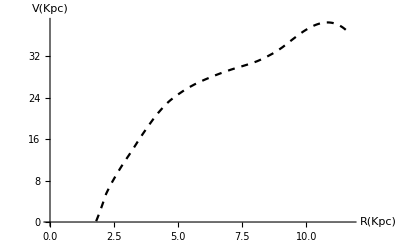

```mathematica
Igas=Interpolation[Subscript[RC, gas]];
Subscript[V^2, gas]=(Igas^2)[r];
Gas= Plot[Igas[x],{x,1.8,11.7},AxesOrigin->{x=0,x=0},PlotStyle->{Black,Dashed},AxesLabel->{"R(Kpc)","V(Kpc)"}]
```

## Gráfico Velocidade das estrelas no disco

```mathematica
Subscript[V, d1]=Plot[√(Subscript[V^2, disk][r])/.{Subscript[R, d]->1.58,Subscript[M, d]->10^9},{r,0,20}] ;
Subscript[V, d2]=Plot[√(Subscript[V^2, disk][r])/.{Subscript[R, d]->1.99,Subscript[M, d]->6.3*10^9},{r,0,30}] ;
Subscript[V, d3]=Plot[√(Subscript[V^2, disk][r])/.{Subscript[R, d]->2.51,Subscript[M, d]->2.5*10^10},{r,0,40}] ;
Subscript[V, d4]=Plot[√(Subscript[V^2, disk][r])/.{Subscript[R, d]->5.01,Subscript[M, d]->10^11},{r,0,50}] ;
Subscript[V, d]=Show[Subscript[V, d1],Subscript[V, d2],Subscript[V, d3],Subscript[V, d4],Frame->True,PlotRange->All,AspectRatio->0.8,PlotLabel->"Estrelas no disco",AxesLabel->{"R(Kpc)","V(Km/s)"}];
```

## Gráfico Velocidade Matéria Escura

```mathematica
Subscript[V, dm1]=Plot[√(Subscript[V^2, Dm][r])/.{Subscript[R, o]->0.32,Subscript[P, o]->4.1 10^8},{r,0,10},PlotRange->All];
Subscript[V, dm2]=Plot[√(Subscript[V^2, Dm][r])/.{Subscript[R, o]->1,Subscript[P, o]->1.05 10^8},{r,0,12},PlotRange->All];
Subscript[V, dm3]=Plot[√(Subscript[V^2, Dm][r])/.{Subscript[R, o]->3.16,Subscript[P, o]->2.5 10^7},{r,0,20},PlotRange->All];
Subscript[V, dm4]=Plot[√(Subscript[V^2, Dm][r])/.{Subscript[R, o]->6.31,Subscript[P, o]->9.7 10^6},{r,0,45},PlotRange->All];
Subscript[V, dm5]=Plot[√(Subscript[V^2, Dm][r])/.{Subscript[R, o]->10,Subscript[P, o]->5.7 10^6},{r,0,60},PlotRange->All];
Subscript[V, dm6]=Plot[√(Subscript[V^2, Dm][r])/.{Subscript[R, o]->15.85,Subscript[P, o]->3.9 10^6},{r,0,70},PlotRange->All];
Subscript[V, dm7]= Plot[√(Subscript[V^2, Dm][r])/.{Subscript[R, o]->25.12,Subscript[P, o]->2.3 10^6},{r,0,100},PlotRange->All];
Subscript[V, dm8]=Plot[√(Subscript[V^2, Dm][r])/.{Subscript[R, o]->39.81,Subscript[P, o]->1.4 10^6},{r,0,125},PlotRange->All];
Show[Subscript[V, dm1],Subscript[V, dm2],Subscript[V, dm3]];
Subscript[V, dm]=Show[Subscript[V, dm4],Subscript[V, dm5],Subscript[V, dm6],Subscript[V, dm7],Subscript[V, dm8], Frame->True,PlotRange->All,AspectRatio->0.75,PlotLabel->"Modelo de Burket para o Halo de Matéria Escura"];
```

## Modelo de Burket ESO 116-G12

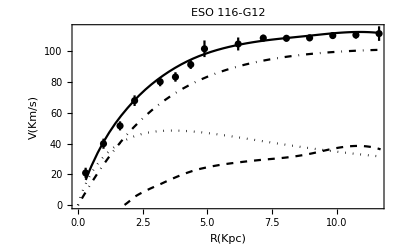

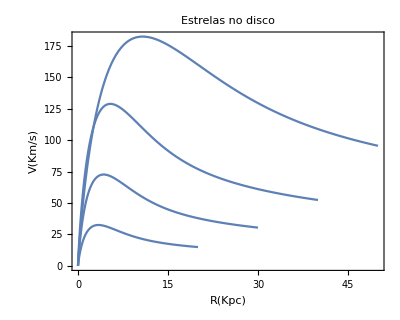
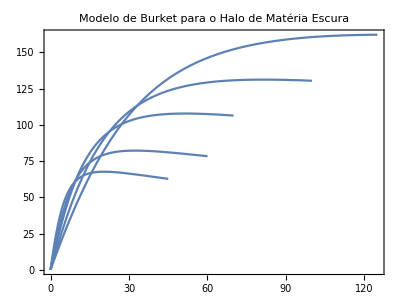

```mathematica
Needs["ErrorBarPlots`"];
Subscript[CR, tot]=ErrorListPlot[{Table[{Subscript[RC, total]⟦i⟧,ErrorBar[Erro⟦i⟧]},{i,15}]},PlotStyle->Black];
Subscript[RC, stars]=Plot[√(Subscript[V^2, disk][r])/.{Subscript[M, d]->2.4 10^9,Subscript[R, d]->1.7},{r,0,11.7},PlotStyle->{Black,Dotted}];
Subscript[RC, halo]=Plot[√(Subscript[V^2, Dm][r])/.{Subscript[R, o]->4.3,Subscript[P, o]->4.7 10^7},{r,0,11.7},PlotStyle->{Black,DotDashed}];
Subscript[RC, vtot]=Plot[Subscript[V, t][r]/.{Subscript[M, d]->2.4 10^9,Subscript[R, d]->1.7,Subscript[R, o]->4.3,Subscript[P, o]->4.7 10^7},{r,0.3,11.6},PlotStyle->Black,PlotRange->Automatic];
Show[Subscript[CR, tot],Subscript[RC, stars],Subscript[RC, halo],Subscript[RC, vtot],Gas,Frame->True,PlotRange->{{0,11.6},{0,115}},PlotLabel->"ESO 116-G12",FrameLabel->{"R(Kpc)","V(Km/s)"}]
Table[{Subscript[V, d],Subscript[V, dm]}]
```

## Ajuste Linear

FittedModel[0.193333+2.1303 x]

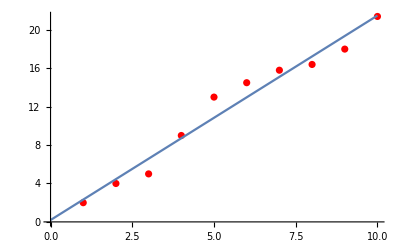

FittedModel[0.193333+2.1303 x]

```mathematica
f[x_,c_,d_]:=c+d*x;
Subscript[data, a] = Table[{2,4,5,9,13,14.5,15.8,16.4,18,21.4}];
LinearModelFit[Subscript[data, a],x,x]
   Ajuste =Show[ListPlot[Subscript[data, a],PlotStyle->Red],Plot[%52[x],{x,0,10}]]
Subscript[Ajuste, 1]=NonlinearModelFit[Subscript[data, a],f[x,c,d],{{c,0.5},{d,3}},x]
Clear[f];
```

FittedModel[1.93982+3.15317 x+2.40117 x^2]

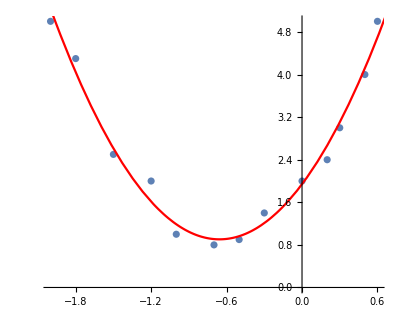

```mathematica
f[x_,a_,b_,c_]:=a+b*x+c*x^2;
Subscript[data, b]_= Table[{{-2,5},{-1.8,4.3},{-1.5,2.5},{-1.2,2},{-1,1},{-0.7,0.8},{-0.5,0.9},{-0.3,1.4},{0,2},{0.2,2.4},{0.3,3},{0.5,4},{0.6,5}}];
Subscript[Fit, 1] =NonlinearModelFit[Subscript[data, b],f[x,b,c,a],{{a,2},{b,4},{c,2}},x]
Show[ListPlot[Subscript[data, b],AspectRatio->0.8],Plot[Subscript[Fit, 1][x],{x,-2,2},PlotStyle->Red]]
Clear[f];
```